# Setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
LaunchKernels[14];
```

```mathematica
Get["C:\\Users\\Miguel\\Github\\Entropy\\Figures_paper\\Degeneracies\\QMB_offline.wl"];
```

SetDelayed::write: Tag Commutator in Commutator[A_,B_] is Protected.

# Degeneracies LRN

```mathematica
L=8;
J=1;
```

```mathematica
visited=ConstantArray[False,2^L,SparseArray];
evenMap={};
oddMap={};
Do[
If[!visited[[i+1]],
j=revIndex[i,L];
visited[[i+1]]=True;
visited[[j+1]]=True;
If[i==j,AppendTo[evenMap,{i}],AppendTo[evenMap,{i,j}];
AppendTo[oddMap,{i,j}];
];]
,{i,0,(2^L)-1}];
```

```mathematica
(*1. Distribute ALL custom functions the parallel kernels will need*)
DistributeDefinitions[IsingHamiltonian,BlockDiagonalize,evenMap,oddMap];
```

```mathematica
hz=0.;
```

```mathematica
(*2. Use ParallelTable instead of ParallelDo+SetSharedVariable*)
data1=ParallelTable[Module[{Ha,system,eveneigenval,oddeigenval,speca},
Ha=-IsingHamiltonian[hx,hz,J,L,BoundaryConditions->"Open"];
system=BlockDiagonalize[Ha,Symmetry->"Parity"];
eveneigenval=Quiet[Eigenvalues[system[[1]]]];
oddeigenval=Quiet[Eigenvalues[system[[2]]]];
speca=Sort[Join[eveneigenval,oddeigenval]];
Transpose[{ConstantArray[hx,2^L],speca}]]
,{hx,0,3,0.0025},Method->"CoarsestGrained"];
```

```mathematica
Range[0,3,0.0025]//Length
```

1201

```mathematica
(*If you need it flattened to match your previous data structure*)
data1=Flatten[data1,1];
```

```mathematica
xs={0.05,0.3,1.0};
```

```mathematica
plot=ListPlot[data1,PlotStyle->Directive[Blue,PointSize[0.00125]],PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,30],PlotLabel->Style["LRN, L = "<>ToString[L]<>", J = "<>ToString[J]<>", g = 0",35,Black],FrameLabel->{Style["h",35,Black],Rotate[Style["E",35,Black],-90Degree]},GridLines->None,PlotRange->All,ImageSize->1200,AspectRatio->0.6,Epilog->{Directive[Red,Dashed,Thick],Table[InfiniteLine[{{x,0},{x,1}}],{x,xs}]},Background->White];
Export["newLRN_levels_g_0_L_"<>ToString[L]<>"_.png",plot];
```

# Degeneracies SRN

```mathematica
L=10;
J=1;
```

```mathematica
visited=ConstantArray[False,2^L,SparseArray];
evenMap={};
oddMap={};
Do[
If[!visited[[i+1]],
j=revIndex[i,L];
visited[[i+1]]=True;
visited[[j+1]]=True;
If[i==j,AppendTo[evenMap,{i}],AppendTo[evenMap,{i,j}];
AppendTo[oddMap,{i,j}];
];]
,{i,0,(2^L)-1}];
```

```mathematica
(*1. Distribute ALL custom functions the parallel kernels will need*)
DistributeDefinitions[IsingHamiltonian,BlockDiagonalize,evenMap,oddMap];
```

```mathematica
hx=1.;
```

```mathematica
(*2. Use ParallelTable instead of ParallelDo+SetSharedVariable*)
data1=ParallelTable[Module[{Ha,system,eveneigenval,oddeigenval,speca},
Ha=-IsingHamiltonian[hx,hz,J,L,BoundaryConditions->"Open"];
system=BlockDiagonalize[Ha,Symmetry->"Parity"];
eveneigenval=Quiet[Eigenvalues[system[[1]]]];
oddeigenval=Quiet[Eigenvalues[system[[2]]]];
speca=Sort[Join[eveneigenval,oddeigenval]];
Transpose[{ConstantArray[hz,2^L],speca}]]
,{hz,0,3,0.005},Method->"CoarsestGrained"];
```

```mathematica
(*If you need it flattened to match your previous data structure*)
data1=Flatten[data1,1];
```

```mathematica
xs={1,2};
```

```mathematica
plot=ListPlot[data1,PlotStyle->Directive[Blue,PointSize[0.00125]],PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,30],PlotLabel->Style["SRN, L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1",35,Black],FrameLabel->{Style["h",35,Black],Rotate[Style["E",35,Black],-90Degree]},GridLines->None,PlotRange->All,ImageSize->1200,AspectRatio->0.6,Epilog->{Directive[Red,Dashed,Thick],Table[InfiniteLine[{{x,0},{x,1}}],{x,xs}]},Background->White];
Export["newSRN_levels_h_1_L_"<>ToString[L]<>"_.png",plot];
```

# Mode basis

```mathematica
(*1. Single-Particle Energies*)
SingleParticleEnergies[L_,h_,J_:1.0]:=Table[2 Sqrt[J^2+h^2-2 J*h*Cos[n*Pi/(L+1)]],{n,1,L}];

(*1. Create a caching function for the structure.The `:=name[L]=` syntax tells Mathematica to remember the result forever after the first time it calculates it for a specific L.*)CachedTopology[L_]:=CachedTopology[L]=Module[{nu,Nqp},nu=Tuples[{0,1},L];
Nqp=Total[nu,{2}];(*Highly optimized matrix-level sum*){nu,Nqp}];

(*2. The streamlined ManyBodySpectrum function*)
Clear[ManyBodySpectrum];
ManyBodySpectrum[eps_List]:=Module[{L,nu,Nqp,E0,Elist},L=Length[eps];
(*Instantly recall the structure from memory instead of rebuilding it*){nu,Nqp}=CachedTopology[L];
E0=-0.5*Total[eps];
Elist=E0+nu.eps;
{Elist,nu,Nqp}];
```

```mathematica
(* ================================================================*)
(*PLOTTING FUNCTIONS*)
(* ================================================================*)

(*Plot 1:Single Particle Energies vs h*)
PlotSingleParticle[L_,hmin_,hmax_,J_:1.0]:=Plot[Evaluate[SingleParticleEnergies[L,h,J]],{h,hmin,hmax},PlotLegends->LineLegend[Automatic,Table["n = "<>ToString[n],{n,1,L}]],AxesLabel->{"h","ϵ(h)"},PlotLabel->"Single-particle energies, L="<>ToString[L]<>", OBC",GridLines->{{J},None},ImageSize->Medium];

(*Plot 2:Many-body Spectrum colored by Quasiparticle Number*)
Clear[PlotManyBodyNqp];
PlotManyBodyNqp[L_,hmin_,hmax_,J_:1.0]:=Module[{epsVar,EVar,NqpVar,colors,cf},
epsVar=SingleParticleEnergies[L,h,J];
{EVar,_,NqpVar}=ManyBodySpectrum[epsVar];
cf=ColorData["DarkRainbow"];
colors=cf[#/L]&/@NqpVar;
Plot[Evaluate[EVar],{h,hmin,hmax},PlotStyle->(Directive[Opacity[0.7],AbsoluteThickness[1],#]&/@colors),AxesLabel->{"h","E"},PlotLabel->"Many-body spectrum ("<>ToString[2^L]<>" levels), L="<>ToString[L],GridLines->{{J},None},LabelStyle->Directive[Black, 25],PlotLegends->BarLegend[{"DarkRainbow",{0,L}},LegendLabel->"Subscript[N, qp]"],ImageSize->800]];

Clear[PlotManyBodyNqpFast];
PlotManyBodyNqpFast[L_,hmin_,hmax_,J_:1.0,Nh_:150]:=Module[{hVals,epsMatrix,EMatrix,NqpVar,colors,cf,plotData},(*1. Create a discrete grid of h values*)hVals=Subdivide[hmin,hmax,Nh-1];
(*2. Evaluate the single particle energies strictly numerically*)epsMatrix=Table[SingleParticleEnergies[L,h,J],{h,hVals}];
(*3. Map our optimized ManyBodySpectrum over the numerical grid*)(*This produces an array of dimensions {Nh,2^L}*)EMatrix=ManyBodySpectrum[#][[1]]&/@epsMatrix;
(*4. Transpose so we have 2^L separate lines to plot*)plotData=Transpose[EMatrix];
(*5. Get Nqp just once for the colors (using dummy h=0)*)NqpVar=ManyBodySpectrum[SingleParticleEnergies[L,0,J]][[3]];
cf=ColorData["DarkRainbow"];
colors=cf[#/L]&/@NqpVar;
(*6. Plot the raw numerical data instantly*)
(*6. Plot the raw numerical data instantly*)ListLinePlot[plotData,DataRange->{hmin,hmax},PlotStyle->(Directive[Opacity[0.7],AbsoluteThickness[1],#]&/@colors),Frame->True,FrameLabel->{"h","E"},(* <---CHANGED THIS*)FrameStyle->Directive[Black,20],(* <---CHANGED THIS*)PlotLabel->"Many-body spectrum ("<>ToString[2^L]<>" levels), L="<>ToString[L],GridLines->{{J},None},LabelStyle->Directive[Black,25],PlotLegends->BarLegend[{"DarkRainbow",{0,L}},LegendLabel->Subscript["N","quasi-part"]],ImageSize->1000]];

(*Plot 3:Degeneracy and Gap Analysis*)
PlotDegeneracyAnalysis[L_,hmin_,hmax_,J_:1.0,Nh_:300]:=Module[{hVals,epsData,gapSP,EData,gapMB,nDistinct},hVals=Subdivide[hmin,hmax,Nh-1];
epsData=SingleParticleEnergies[L,#,J]&/@hVals;
gapSP=Min/@epsData;
EData=ManyBodySpectrum[#][[1]]&/@epsData;
gapMB=Table[With[{sorted=Sort[EData[[i]]]},sorted[[2]]-sorted[[1]]],{i,Length[hVals]}];
nDistinct=Length[DeleteDuplicates[Round[#,10^-8]]]&/@EData;
GraphicsRow[{ListLinePlot[Transpose[{hVals,gapSP}],AxesLabel->{"h","Subscript[ϵ, 1](h)"},PlotLabel->"(a) Single-particle gap",GridLines->{{J},None}],ListLinePlot[Transpose[{hVals,gapMB}],AxesLabel->{"h","ΔE"},PlotStyle->Red,PlotLabel->"(b) Many-body gap",GridLines->{{J},None}],ListLinePlot[Transpose[{hVals,nDistinct}],AxesLabel->{"h","# distinct levels"},PlotStyle->Black,PlotLabel->"(c) Degeneracy count",GridLines->{{J},None},Epilog->{Dashed,Gray,InfiniteLine[{0,2^L},{1,0}]}]},ImageSize->1200]];

(*Plot 4:Dispersion Relation (Energy vs Momentum k)*)
(*Shows discrete finite-size points over the continuous thermodynamic limit*)
PlotDispersionVsK[h_,Llist_List,J_:1.0]:=Module[{kData,contPlot,discPlot},(*Generate discrete {k,ϵ(k)} points for each L in the list*)kData=Table[Table[{n*Pi/(L+1),2 Sqrt[J^2+h^2-2 J*h*Cos[n*Pi/(L+1)]]},{n,1,L}],{L,Llist}];
(*Plot the continuous theoretical curve (L->∞)*)contPlot=Plot[2 Sqrt[J^2+h^2-2 J*h*Cos[k]],{k,0,Pi},PlotStyle->Directive[Gray,Dashed,AbsoluteThickness[1.5]],PlotLegends->{"L → ∞ (Continuous)"}];
(*Plot the discrete points for the specific L values*)discPlot=ListPlot[kData,PlotMarkers->Automatic,PlotStyle->PointSize[0.015],PlotLegends->("L = "<>ToString[#]&/@Llist)];
(*Combine them*)Show[contPlot,discPlot,AxesLabel->{"Momentum (k)","Energy ϵ(k)"},PlotLabel->"Dispersion Relation (h = "<>ToString[h]<>", J = "<>ToString[J]<>")",GridLines->Automatic,ImageSize->Large,BaseStyle->{FontSize->14}]];
```

## plotting

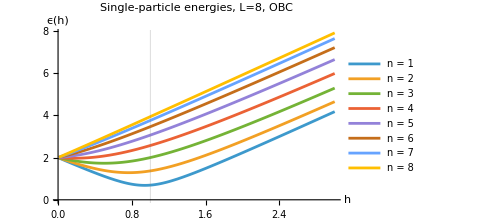

```mathematica
(*To plot the single particle spectrum for L=8 from h=0.01 to h=3*)
PlotSingleParticle[8,0.01,3]
```

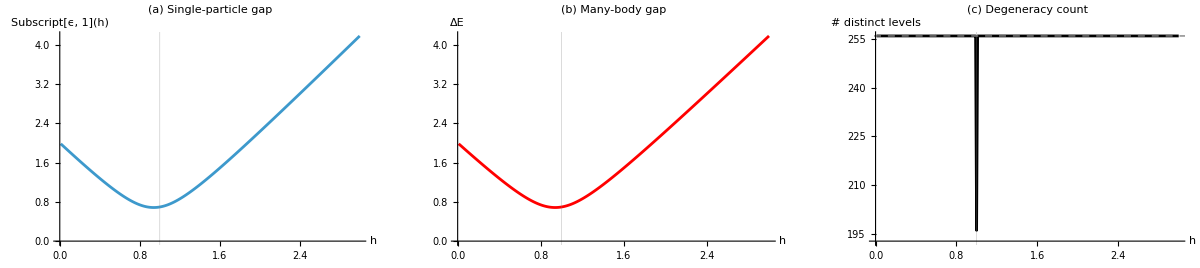

```mathematica
(*To plot the degeneracy and gap analysis*)
PlotDegeneracyAnalysis[8,0.01,3]
```

```mathematica
(*To plot the full many-body spectrum for L=8*)
plot=PlotManyBodyNqpFast[8,0,3]
Export["many_body_spectrum_TFIM.png",plot,ImageResolution->300];
```

-Graphics-

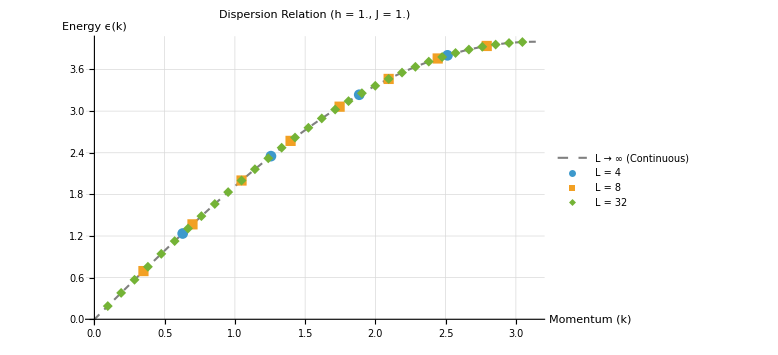

```mathematica
PlotDispersionVsK[1.0,{4,8,32}]
```

## Periodic boundary conditions

```mathematica
(* ================================================================*)(*FULL BOGOLIUBOV BAND STRUCTURE (THERMODYNAMIC LIMIT)*)(* ================================================================*)PlotFullBands[h_,J_:1.0]:=Plot[{2 Sqrt[J^2+h^2-2 J*h*Cos[k]],(*Particle band (+E)*)-2 Sqrt[J^2+h^2-2 J*h*Cos[k]]   (*Hole band (-E)*)},{k,-Pi,Pi},PlotStyle->{Directive[Thick,Blue],Directive[Thick,Red]},PlotRange->{{-Pi,Pi},{-4.5 J,4.5 J}},Ticks->{{-Pi,-Pi/2,0,Pi/2,Pi},Automatic},AxesLabel->{"Momentum (k)","Energy ϵ(k)"},PlotLabel->"Full Bogoliubov Bands (h = "<>ToString[h]<>", J = "<>ToString[J]<>")",Filling->{1->{2}},(*Shading between the bands to highlight the gap*)FillingStyle->Directive[Opacity[0.1],Blue],GridLines->Automatic,ImageSize->Large,BaseStyle->{FontSize->14}];
```

```mathematica
(*---INTERACTIVE SLIDER (Highly Recommended)---*)
Manipulate[Plot[{2 Sqrt[J^2+h^2-2 J*h*Cos[k]],-2 Sqrt[J^2+h^2-2 J*h*Cos[k]]},{k,-Pi,Pi},PlotStyle->{Directive[Thick,Blue],Directive[Thick,Red]},PlotRange->{{-Pi,Pi},{-4.5,4.5}},Ticks->{{-Pi,-Pi/2,0,Pi/2,Pi},Automatic},AxesLabel->{"Momentum (k)","Energy ϵ(k)"},PlotLabel->"Gap Δ = "<>ToString[NumberForm[2 Abs[J-h],{3,2}]],Filling->{1->{2}},FillingStyle->Directive[Opacity[0.1],Blue],GridLines->Automatic,ImageSize->Large,BaseStyle->{FontSize->14}],{{h,0.5,"Magnetic Field (h)"},0,3,Appearance->"Labeled"},{{J,1.0,"Ising Coupling (J)"},0.1,2,Appearance->"Labeled"},TrackedSymbols:>{h,J}]
```

```mathematica
(* ================================================================*)(*FINITE SIZE BOGOLIUBOV BANDS (DISCRETE MOMENTUM POINTS)*)(* ================================================================*)Manipulate[Module[{kDiscrete,epsDiscrete,contPlot,discPlot},(*1. Calculate the discrete momentum points allowed for finite L (OBC)*)(*We include both+k and-k to show the full symmetric Brillouin zone*)kDiscrete=Flatten[Table[{n*Pi/(L+1),-n*Pi/(L+1)},{n,1,L}]];
(*2. Calculate the energy at exactly those discrete points*)epsDiscrete=2 Sqrt[J^2+h^2-2 J*h*Cos[kDiscrete]];
(*3. Plot the continuous thermodynamic limit as a faint background shadow*)contPlot=Plot[{2 Sqrt[J^2+h^2-2 J*h*Cos[k]],-2 Sqrt[J^2+h^2-2 J*h*Cos[k]]},{k,-Pi,Pi},PlotStyle->{Directive[Thick,Opacity[0.3],Blue],Directive[Thick,Opacity[0.3],Red]},Filling->{1->{2}},FillingStyle->Directive[Opacity[0.05],Blue]];
(*4. Plot the discrete points for our specific finite L on top*)discPlot=ListPlot[{Transpose[{kDiscrete,epsDiscrete}],(*Particle points (+E)*)Transpose[{kDiscrete,-epsDiscrete}]   (*Hole points (-E)*)},PlotStyle->{Directive[PointSize[0.015],Blue],Directive[PointSize[0.015],Red]}];
(*Combine and display*)Show[contPlot,discPlot,PlotRange->{{-Pi-0.2,Pi+0.2},{-4.5 J,4.5 J}},Ticks->{{-Pi,-Pi/2,0,Pi/2,Pi},Automatic},AxesLabel->{"Momentum (k)","Energy ϵ(k)"},PlotLabel->"Finite Size Bands (L = "<>ToString[L]<>", h = "<>ToString[NumberForm[h,{3,2}]]<>")",GridLines->Automatic,ImageSize->Large,BaseStyle->{FontSize->14}]],(*Sliders for interactivity*){{h,1.0,"Magnetic Field (h)"},0,3,Appearance->"Labeled"},{{L,8,"System Size (L)"},2,64,1,Appearance->"Labeled"},{{J,1.0,"Ising Coupling (J)"},0.1,2,Appearance->"Labeled"},TrackedSymbols:>{h,L,J}]
```

# Free fermions

```mathematica
(* ================================================================*)(*EXACT FINITE-SIZE SINGLE PARTICLE ENERGIES (OBC BdG)*)(* ================================================================*)Clear[ExactSingleParticleEnergies];
ExactSingleParticleEnergies[L_,h_,J_:1.0]:=Module[{A,B,HBdG,evals,posEvals},
(*1. Construct the L x L A matrix (Symmetric:Hopping+Field)*)A=Table[If[i==j,2 h,If[Abs[i-j]==1,-J,0]],{i,1,L},{j,1,L}];
(*2. Construct the L x L B matrix (Anti-symmetric:Pairing)*)B=Table[If[j==i+1,-J,If[i==j+1,J,0]],{i,1,L},{j,1,L}];
(*3. Build the 2L x 2L BdG Block Matrix*)HBdG=ArrayFlatten[{{A,B},{-B,-A}}];
(*4. Numerically find eigenvalues.(//N forces fast machine-precision math)*)evals=Eigenvalues[HBdG//N];
(*5. Sort the 2L eigenvalues and take only the top L (the positive ones)*)posEvals=Take[Sort[evals],-L];
Return[posEvals];];
```

```mathematica
(*The Many-Body Constructor (Unchanged)*)
CachedTopology[L_]:=CachedTopology[L]=Module[{nu,Nqp},nu=Tuples[{0,1},L];Nqp=Total[nu,{2}];{nu,Nqp}];

Clear[ManyBodySpectrum];
ManyBodySpectrum[eps_List]:=Module[{L,nu,Nqp,E0,Elist},L=Length[eps];
{nu,Nqp}=CachedTopology[L];
E0=-0.5*Total[eps];
Elist=E0+nu.eps;
{Elist,nu,Nqp}];

(*The Plotting Function*)
Clear[PlotExactSpectrum];
PlotExactSpectrum[L_,hmin_,hmax_,J_:1.0,Nh_:150]:=Module[{hVals,epsMatrix,EMatrix,NqpVar,colors,cf,plotData},hVals=Subdivide[hmin,hmax,Nh-1];
(*USE THE NEW EXACT FUNCTION HERE*)epsMatrix=Table[ExactSingleParticleEnergies[L,h,J],{h,hVals}];
EMatrix=ManyBodySpectrum[#][[1]]&/@epsMatrix;
plotData=Transpose[EMatrix];
NqpVar=ManyBodySpectrum[ExactSingleParticleEnergies[L,0,J]][[3]];
cf=ColorData["DarkRainbow"];
colors=cf[#/L]&/@NqpVar;
ListLinePlot[plotData,DataRange->{hmin,hmax},PlotStyle->(Directive[Opacity[0.7],AbsoluteThickness[1],#]&/@colors),Frame->True,FrameLabel->{"h","E"},FrameStyle->Directive[Black,20],PlotLabel->"Free-Fermion Spectrum (L="<>ToString[L]<>")",GridLines->{{J},None},LabelStyle->Directive[Black,25],PlotLegends->BarLegend[{"DarkRainbow",{0,L}},LegendLabel->Subscript["N","qp"]],ImageSize->1200]];
```

```mathematica
plot=PlotExactSpectrum[8,0,3]
Export["exact_diagonalization_TFIM.png",plot]
```

-Graphics-

exact_diagonalization_TFIM.png